```mathematica
Clear[α,β];

nuPK=2.07; BuPK=0.5;    αuPK=0.3;  αuPK'=0.45;  βu=4; (* 11.p8.f *)
ndPK= 1.35; BdPK=0.5;   αdPK=  0.3; αdPK'=0.45;   βd=5;    

nu11=2.65081;  Bu11=-0.19838;     αu11=0.117335;    αu11'=0.685104;  βu=4; (* 11.p8.f *)
nd11= 1.41006; Bd11=-0.397028;   αd11=  0.34777;     αd11'=1.34889;   βd=5;    

nu31=3.16891; Bu31=0.283963;   αu31=0.023355;  αu31'=0.553622;  βu=4; (* 31.p8.f *)
nd31=8.50422; Bd31=-1.39061;   αd31= -6.76073;     αd31'=15.265;   βd=5;    

nu14f=2.51288;  Bu14f=-0.0471231;     αu14f=0.0895733;    αu14f'=0.610796;  βu=4; (* 14.p8.f *)
nd14f= 1.66733; Bd14f=-1.2884;   αd14f=  0.447876;     αd14f'=1.34889;   βd=5;    

nu14t=2.59718; Bu14t=0.405811;   αu14t=-0.0276665;  αu14t'=1.55215;  βu=4; (* 14.p8.t *)
nd14t=1.47267; Bd14t=-0.51516;   αd14t= 0.182535;     αd14t'=1.25344;   βd=5;    
 
norma[α_,β_]:=(Gamma[1-α] Gamma[1+β])/Gamma[2-α+β];


ETPF[x_,B_,αp_]:=(B+αp Log[1./x]);
ETFL[x_,n_,α_,β_]:=n*x^(-α)*(1.-x)^β;
ET[x_,t_,n_,B_,α_,αp_,β_]:=ETFL[x,n,α,β]*Exp[ETPF[x,B,αp]*t]/norma[α,β];

ETuPK[x_,t_]:=ET[x,t,nuPK,BuPK,αuPK,αu11',βu];
ETdPK[x_,t_]:=ET[x,t,ndPK,BdPK,αdPK,αd11',βd];

ETu11[x_,t_]:=ET[x,t,nu11,Bu11,αu11,αu11',βu];
ETd11[x_,t_]:=ET[x,t,nd11,Bd11,αd11,αd11',βd];

ETu31[x_,t_]:=ET[x,t,nu31,Bu31,αu31,αu31',βu];
ETd31[x_,t_]:=ET[x,t,nd31,Bd31,αd31,αd31',βd];


 x1=0.1; x2=0.2; x3=0.3; x4=0.4; x5=0.5;
tmin=0; tmax=2.0;
```

```mathematica
(*    11.P8.f *)
Plot1101=Plot[{ETu11[x1,-t],ETd11[x1,-t]} ,                {t,tmin,tmax},
PlotLabel->"11.p8.f  x=0.1",
FrameLabel->{"-t","ETbar"},
PlotRange->{{tmin,tmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"-t"," "},
PlotStyle->{Blue,Red}];
Plot1102=Plot[{ETu11[x2,-t],ETd11[x1,-t]} ,                {t,tmin,tmax},
PlotLabel->"11.p8.f x=0.2",
FrameLabel->{"-t","ETbar"},
PlotRange->{{tmin,tmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"-t"," "},
PlotStyle->{Blue,Red}];
Plot1103=Plot[{ETu11[x3,-t],ETd11[x1,-t]} ,                {t,tmin,tmax},
PlotLabel->"11.p8.f x=0.3",
FrameLabel->{"-t","ETbar"},
PlotRange->{{tmin,tmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"-t"," "},
PlotStyle->{Blue,Red}];
Plot1104=Plot[{ETu11[x4,-t],ETd11[x1,-t]} ,                {t,tmin,tmax},
PlotLabel->"11.p8.f x=0.4",
FrameLabel->{"-t","ETbar"},
PlotRange->{{tmin,tmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"-t"," "},
PlotStyle->{Blue,Red}];

(*    31.P8.f *)
Plot3101=Plot[{ETu31[x1,-t],ETd31[x1,-t]} ,                {t,tmin,tmax},
PlotLabel->"31.p8.f x=0.1",
FrameLabel->{"-t"," "},
PlotRange->{{tmin,tmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"-t"," "},
PlotStyle->{Blue,Red}];
Plot3102=Plot[{ETu31[x2,-t],ETd31[x1,-t]} ,                {t,tmin,tmax},
PlotLabel->"31.p8.f x=0.2",
FrameLabel->{"-t"," "},
PlotRange->{{tmin,tmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"-t"," "},
PlotStyle->{Blue,Red}];
Plot3103=Plot[{ETu31[x3,-t],ETd31[x1,-t]} ,                {t,tmin,tmax},
PlotLabel->"31.p8.f x=0.3",
FrameLabel->{"-t"," "},
PlotRange->{{tmin,tmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"-t"," "},
PlotStyle->{Blue,Red}];
Plot3104=Plot[{ETu31[x4,-t],ETd31[x1,-t]} ,                {t,tmin,tmax},
PlotLabel->"31.p8.f x=0.4",
FrameLabel->{"-t"," "},
PlotRange->{{tmin,tmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"-t"," "},
PlotStyle->{Blue,Red}];

(*  Peter original model  *)
PlotPK01=Plot[{ETuPK[x1,-t],ETdPK[x1,-t]} ,                {t,tmin,tmax},
PlotLabel->"PK x=0.1",
FrameLabel->{"-t"," "},
PlotRange->{{tmin,tmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"-t"," "},
PlotStyle->{Blue,Red}];
PlotPK02=Plot[{ETuPK[x2,-t],ETdPK[x1,-t]} ,                {t,tmin,tmax},
PlotLabel->"PK x=0.2",
FrameLabel->{"-t"," "},
PlotRange->{{tmin,tmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"-t"," "},
PlotStyle->{Blue,Red}];
PlotPK03=Plot[{ETuPK[x3,-t],ETdPK[x1,-t]} ,                {t,tmin,tmax},
PlotLabel->"PK x=0.3",
FrameLabel->{"-t"," "},
PlotRange->{{tmin,tmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"-t"," "},
PlotStyle->{Blue,Red}];
PlotPK04=Plot[{ETuPK[x4,-t],ETdPK[x1,-t]} ,                {t,tmin,tmax},
PlotLabel->"PK x=0.4",
FrameLabel->{"-t"," "},
PlotRange->{{tmin,tmax},{0,All}},
Filling->Axis,
Axes->True,AxesLabel->{"-t"," "},
PlotStyle->{Blue,Red}];
```

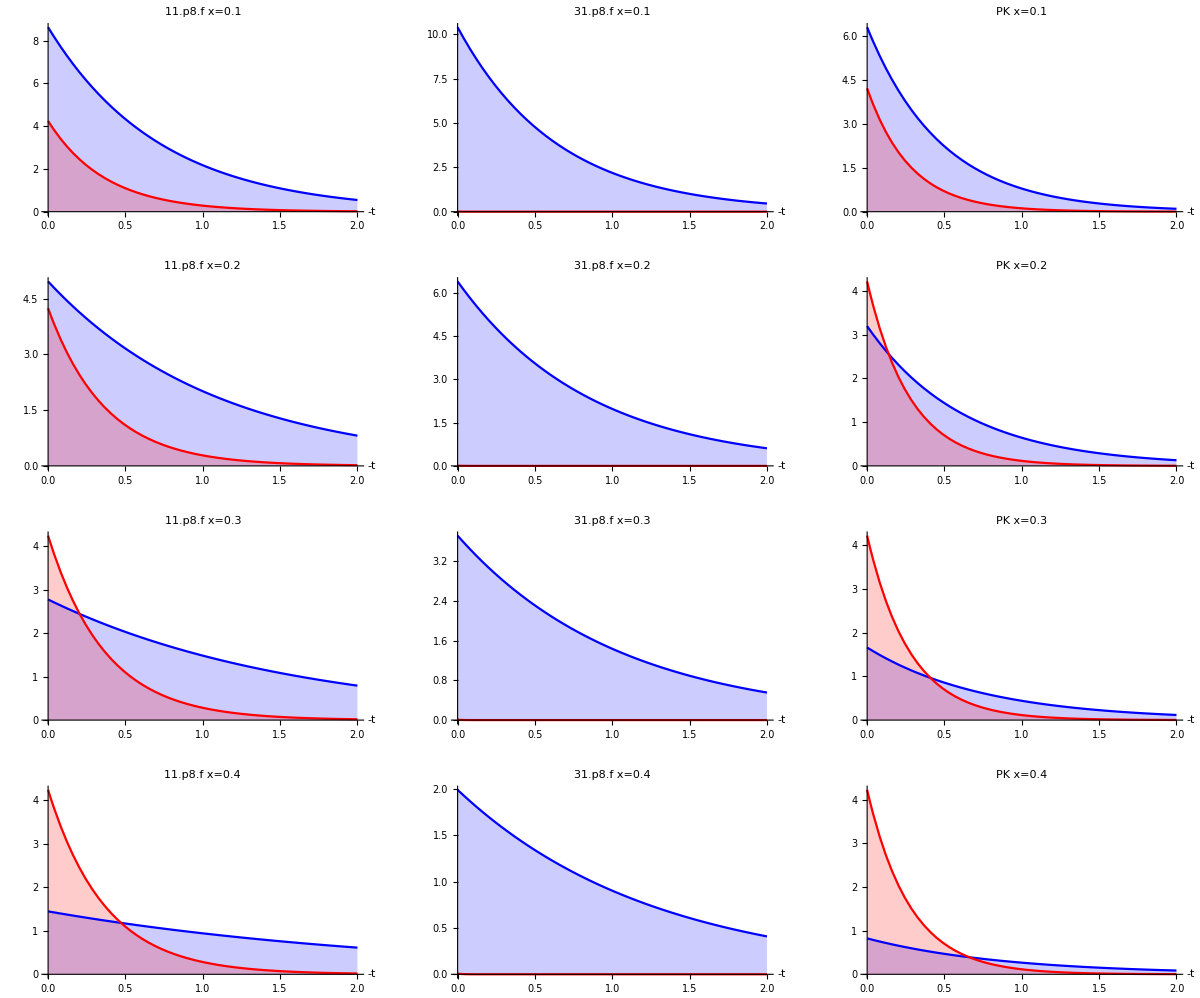

```mathematica
GraphicsGrid[{{Plot1101,Plot3101,PlotPK01},{Plot1102,Plot3102,PlotPK02},{Plot1103,Plot3103,PlotPK03},{Plot1104,Plot3104,PlotPK04}},ImageSize->Full]
```